```mathematica
ClearAll["Global`*"]
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"out", "schaeferTurek"}]]
```

/home/florian/Projects/university/masters_thesis/code/2D/out/schaeferTurek

```mathematica
srts = Complement[FileNames[], FileNames["*time"], FileNames["cumulant*"]];
cumulants = Complement[FileNames[], FileNames["*time"], FileNames["srt*"]];
srtAuxiliary = Complement[FileNames["*time"], FileNames["cumulant*"]];
cumulantAuxiliary = Complement[FileNames["*time"], FileNames["srt*"]];
getSizes[thelist_]:=Read[StringToStream[#],Number]&/@Flatten[ StringDrop[#,4] &/@StringCases[thelist, RegularExpression["size([0-9]*)"]]] 
sizes = getSizes[srts];
permutations = Ordering[sizes];
permutationsAuxiliary = Ordering[getSizes[srtAuxiliary]];
sizes = sizes[[permutations]];
cumulants = cumulants[[permutations]];
srts = srts[[permutations]];
cumulantAuxiliary = cumulantAuxiliary[[permutationsAuxiliary]];
srtAuxiliary = srtAuxiliary[[permutationsAuxiliary]];
```

```mathematica
dragData[input_] := Drop[Map[Delete[#,3]&,input],00];
liftData[input_] := Drop[Map[Delete[#,2]&,input],00];
valuesOnly[data_]:=Flatten[Map[Delete[#,1]&,data]];
myImport[list_] := (Drop[#,1]&/@Import /@ list)*sizes/(sizes-1); (* correcting factor at the end, because I did not incorporate the real size of the sphere in the code. *)
dataFrequency[list_] := Abs[Fourier[ #[[2]]&/@list]];


maximaPositions[list_] :=1+Position[Differences[Sign[Differences[list[[All,2]]]]],-2];
minimaPositions[list_] :=1+Position[Differences[Sign[Differences[list[[All,2]]]]],2]

lastWavelimits[data_]:=Flatten[ Take[maximaPositions[data],-2]];
lastWavelength[data_]:=Differences[lastWavelimits[data]][[1]];

lastWave[data_]  := Take[data,lastWavelimits[data]];
dragResult = 5.8190;
liftResult = 0.0110;
schaefferTurekX = {1314720,332640,85140};
schaefferTurekDrag = {5.8190,5.7740,5.7890};
schaefferTurekLift = {0.0110,0.0030,-0.0060};

means[datas_] := Map[Mean[valuesOnly[#]]&,datas];

liftMeansCumulant := means[lastWave /@liftData /@myImport[cumulants]];
liftMeansSRT := means[lastWave /@liftData /@myImport[srts]];
dragMeansCumulant := means[lastWave /@dragData /@myImport[cumulants]];
dragMeansSRT := means[lastWave /@dragData /@myImport[srts]];

cumulantSizes := Flatten[Drop[#,1]&/@Import[#,"CSV"] &/@ cumulantAuxiliary]
SRTSizes:=Flatten[Drop[#,1]&/@Import[#,"CSV"] &/@ srtAuxiliary]

cumulantTimes := Flatten[Take[#,1]&/@Import[#,"CSV"] &/@ cumulantAuxiliary]
SRTTimes:=Flatten[Take[#,1]&/@Import[#,"CSV"] &/@ srtAuxiliary]

bothLiftMeansPlotReady := {Transpose[{sizes,liftMeansCumulant-liftResult}],Transpose[{sizes,liftMeansSRT-liftResult}]};
bothDragMeansPlotReady := {Transpose[{sizes,dragMeansCumulant-dragResult}],Transpose[{sizes,dragMeansSRT-dragResult}]};
bothLiftMeansPlotReadyVSGridWithTurek := {Transpose[{cumulantSizes,liftMeansCumulant-liftResult}],Transpose[{cumulantSizes,liftMeansSRT-liftResult}], Transpose[{schaefferTurekX,schaefferTurekLift - liftResult}]};
bothLiftMeansPlotReadyVSGrid := {Transpose[{cumulantSizes,liftMeansCumulant-liftResult}],Transpose[{cumulantSizes,liftMeansSRT-liftResult}]};
bothDragMeansPlotReadyVSGridWithTurek := {Transpose[{cumulantSizes,dragMeansCumulant-dragResult}],Transpose[{cumulantSizes,dragMeansSRT-dragResult}], Transpose[{schaefferTurekX,schaefferTurekDrag - dragResult}]};
bothLiftMeansPlotReadyVSTime := {Transpose[{cumulantTimes,liftMeansCumulant-liftResult}],Transpose[{SRTTimes,liftMeansSRT-liftResult}]};bothDragMeansPlotReadyVSTime := {Transpose[{cumulantTimes,dragMeansCumulant-dragResult}],Transpose[{SRTTimes,dragMeansSRT-dragResult}]};
```

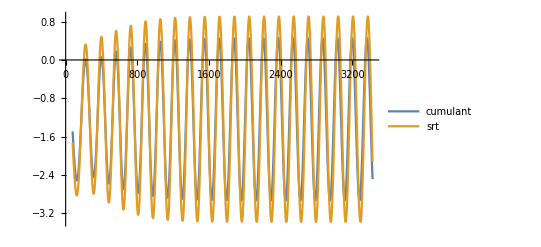

```mathematica
nr=6;
ListLinePlot[{(liftData/@myImport[cumulants])[[nr]],(liftData/@myImport[srts])[[nr]]} , PlotLegends->{"cumulant","srt"}]
```

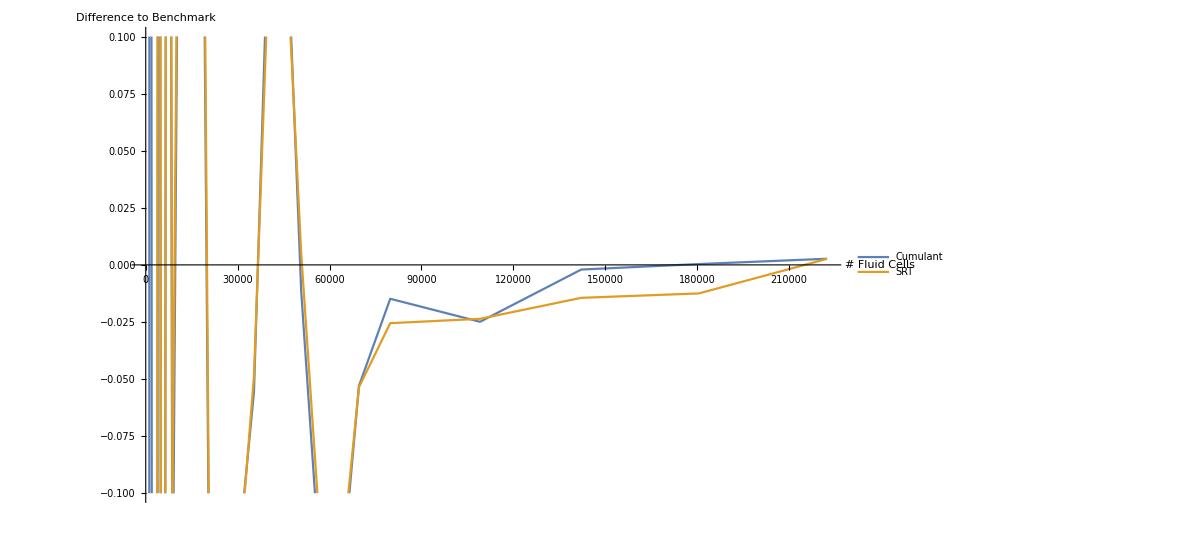

```mathematica
ListLinePlot[bothLiftMeansPlotReadyVSGrid, PlotLegends->Placed[{"Cumulant","SRT"},{Right,Top}], PlotRange->{-0.1,0.1},AxesLabel->{"# Fluid Cells","Difference to Benchmark"}]
```

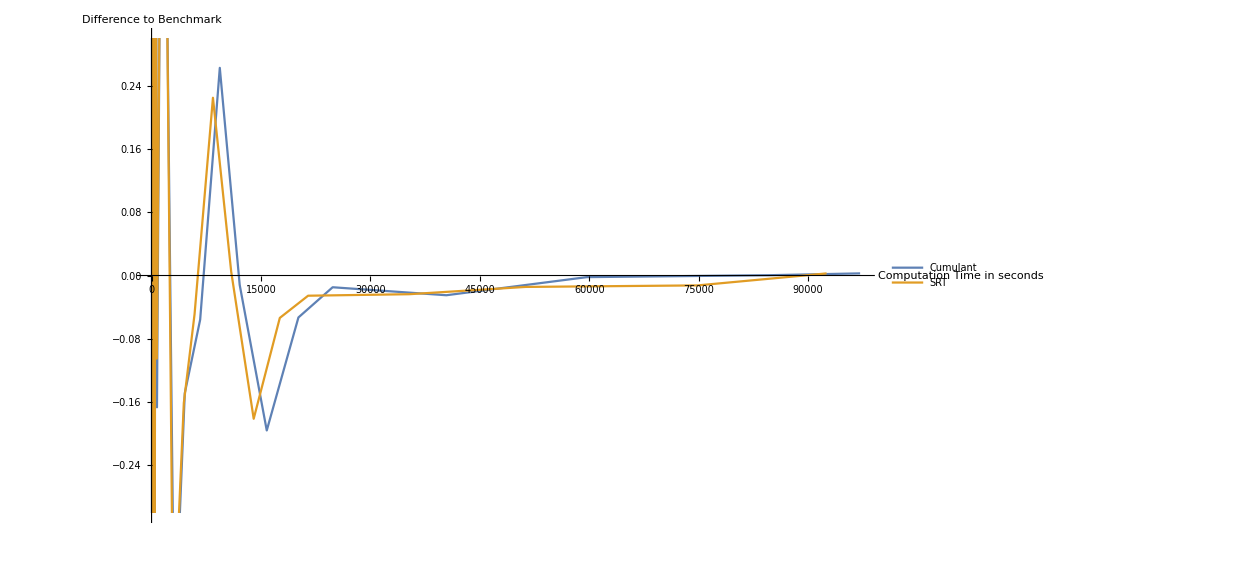

```mathematica
ListLinePlot[bothLiftMeansPlotReadyVSTime,PlotLegends->Placed[{"Cumulant","SRT", "schaefferTurek"},{Right,Top}],PlotRange->{-0.3,0.3},AxesLabel->{"Computation Time
in seconds","Difference to Benchmark"}]
```

```mathematica
ListLinePlot[{Transpose[{cumulantSizes, cumulantTimes}],Transpose[{SRTSizes, SRTTimes}]}, PlotLegends->Placed[{"Cumulant","SRT"},{Right,Center}], AxesLabel->{"","Computation
time in
seconds"}]
```

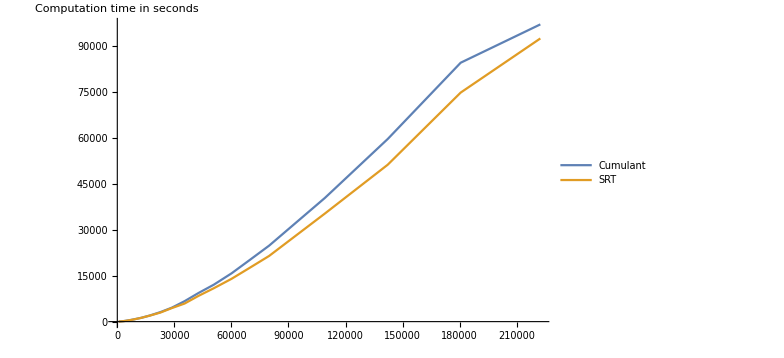

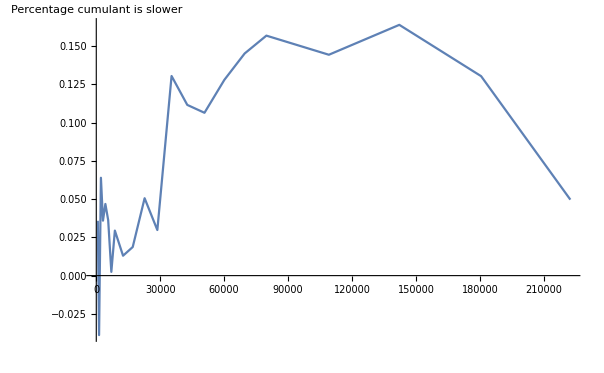

```mathematica
ListLinePlot[Transpose[{cumulantSizes, (cumulantTimes-SRTTimes)/SRTTimes}],AxesLabel->{"","Percentage
cumulant
is slower"}]
```